# Homework assignment 2

Kyle McGraw <kmcgraw@caltech.edu>

## Explore models of computation

Part 1: My understanding of this homework is that I should choose an exercise given below or create my own exercise that will help me gain more familiarity with Mathematica and more familiarity with the different models of computation. Part 1 is just this paragraph of my understanding of the homework and part 2 is the Mathematica exercise. In total the homework should take around 6 hours and should be turned in using a single, self-contained Mathematica notebook with full explanations.

Part 2: Write a program in each model, or say your favorite three models.  Choose your own tasks (could be the same for each model, could be different) or select (or generalize) tasks that were chosen as examples.   E.g. Write a PPM program that copies a binary string, or a PPM program that copies an arbitrary connected graph.  Keep it simple!

Program 1: My first program will be creating a cellular automaton called “Star Wars”. It has the update rule “B2/S345/4”: a new cell is born when a dead cell is surrounded by 2 live cells, and a living cell Survives when it is surrounded by 3, 4, or 5 other living cells, and after a cell dies there are two time steps that they spend in a refractory period.

```mathematica
OneStepCA[f_,cells_]:=With[{N=Length[cells],M=Length[First[cells]]},
BlockMap[f,cells[[{-1}~Join~Range[1,N]~Join~{1},{-1}~Join~Range[1,M]~Join~{1}]],{3,3},{1,1}]]
```

A = active cell, R1 = refractory stage 1 cell, R2 = refractory stage 2 cell, Q = quiescent cell

```mathematica
Clear[A,Q,R1,R2,starwarsCA]
```

```mathematica
starwarsCA[m_]:=With[{self=m[[2,2]],count=Count[Flatten[m],A]-If[m[[2,2]]===A,1,0]},If[(count==2&&self===Q)||(count==3&&self===A)||(count==4&&self===A)||(count==5&&self===A),A,If[self===A,R1,If[self===R1,R2,Q]]]]
```

A stable 5 cell “planet” conformation

```mathematica
planet={{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,A,Q,Q,Q},{Q,Q,A,A,A,Q,Q},{Q,Q,Q,A,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q}}
```

{{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,A,Q,Q,Q},{Q,Q,A,A,A,Q,Q},{Q,Q,Q,A,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q}}

```mathematica
Dynamic[planet=OneStepCA[starwarsCA,planet];ArrayPlot[planet,ColorRules->{A->Red,Q->White,R1->Blue,R2->Green}]]
```

A stable 5 cell “planet” conformation with a “satellite” orbiting it

```mathematica
satellite={{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,A,Q,Q,Q},{Q,Q,A,A,A,Q,Q},{Q,A,Q,A,Q,Q,Q},{Q,Q,R1,R2,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q}}
```

{{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,A,Q,Q,Q},{Q,Q,A,A,A,Q,Q},{Q,A,Q,A,Q,Q,Q},{Q,Q,R1,R2,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q}}

```mathematica
Dynamic[satellite=OneStepCA[starwarsCA,satellite];ArrayPlot[satellite,ColorRules->{A->Red,Q->White,R1->Blue,R2->Green}]]
```

A “glider” that moves across the screen

```mathematica
glider1={{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,A,Q,Q,A},{Q,Q,Q,Q,A,A,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q}}
```

{{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,A,Q,Q,A},{Q,Q,Q,Q,A,A,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q}}

```mathematica
Dynamic[glider1=OneStepCA[starwarsCA,glider1];ArrayPlot[glider1,ColorRules->{A->Red,Q->White,R1->Blue,R2->Green}]]
```

A different type of “glider” that moves across the screen

```mathematica
glider2={{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,A},{Q,Q,Q,Q,Q,A,R1},{Q,Q,Q,Q,A,R1,R2},{Q,Q,Q,Q,A,R1,R2},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q}}
```

{{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,A},{Q,Q,Q,Q,Q,A,R1},{Q,Q,Q,Q,A,R1,R2},{Q,Q,Q,Q,A,R1,R2},{Q,Q,Q,Q,Q,Q,Q},{Q,Q,Q,Q,Q,Q,Q}}

```mathematica
Dynamic[glider2=OneStepCA[starwarsCA,glider2];ArrayPlot[glider2,ColorRules->{A->Red,Q->White,R1->Blue,R2->Green}]]
```

A random generation

```mathematica
starwarsfield=RandomChoice[{Q,A},{100,100}];
```

```mathematica
Dynamic[starwarsfield=OneStepCA[starwarsCA,starwarsfield];ArrayPlot[starwarsfield,ColorRules->{A->Red,Q->White,R1->Blue,R2->Green}]]
```

Program 2: My second program will be creating a graph rewriting grammar, with O(k) rules and O(k) label types, that grows into square grid of size O(2^k) when started with a single node. For this model, there is a slight bug where an error is shown because a rule is chosen that requires more vertices than currently in the graph (because we choose rules at random); however, this bug does not have an impact as the code can keep running and choosing other rules at random.

```mathematica
ApplyGraphRule[G_,Rule[LHS_,RHS_],vertices_]:=Module[{sG=Subgraph[G,vertices],mapping=MapThread[Rule,{VertexList[LHS],vertices}]},
If[VertexCount[LHS]!=VertexCount[sG] || 
(vertices/.AnnotationValue[G,VertexLabels])=!= (VertexList[LHS]/.AnnotationValue[LHS,VertexLabels])||
(Sort/@EdgeList[sG])=!=(Sort/@(EdgeList[LHS]/.mapping)),
G, (* not applicable *)
nG=EdgeDelete[G,EdgeList[LHS]/.mapping];
nG=VertexDelete[nG,Complement[VertexList[LHS],VertexList[RHS]]/.mapping];
newvertices=Complement[VertexList[RHS],VertexList[LHS]];
newmapping=mapping~Join~MapThread[Rule,{newvertices,Max[VertexList[G]]+Range[Length[newvertices]]}];
nG=VertexAdd[nG,newvertices/.newmapping];
nG=Fold[Annotate[{#1,#2[[1]]},VertexLabels->#2[[2]]]&,nG,Transpose[{VertexList[RHS]/.newmapping,VertexList[RHS]/.AnnotationValue[RHS,VertexLabels]}]];
nG=EdgeAdd[nG,EdgeList[RHS]/.newmapping];
nG]
]
```

```mathematica
GraphGrammarSteps[G_,rules_,steps_]:=Module[{n=VertexCount[G],state=G},
Do[
With[{rule=RandomChoice[rules]},
state=ApplyGraphRule[state,rule,RandomSample[VertexList[state],VertexCount[First[rule]]]]],
steps];
state
]
```

This is my first attempt at the challenge. This set of rules create an infinitely growing grid that is not square. Gets stuck in one of the dimension but not sure how to grow that way without running into issues with extra edges being create inside the grid where we don’t want them. Also do not believe this strategy will have the correct size for amount variables and rules needed if I wanted to make a specific sized grid.

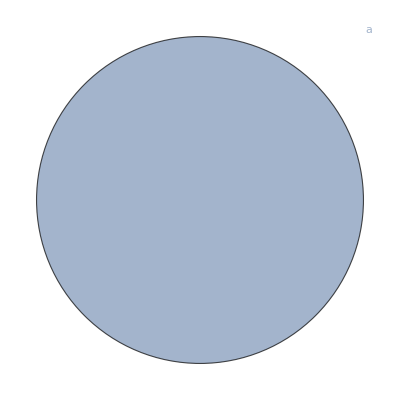
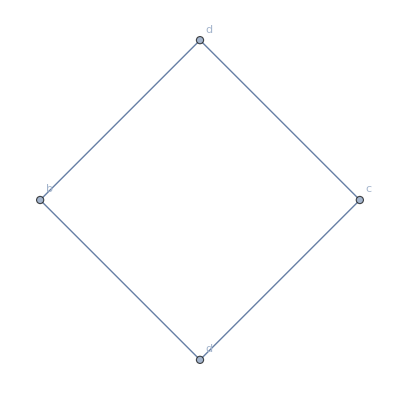
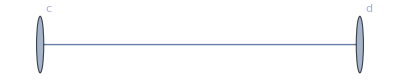
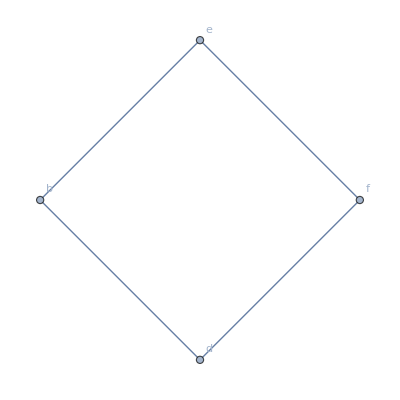
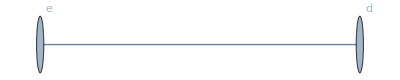
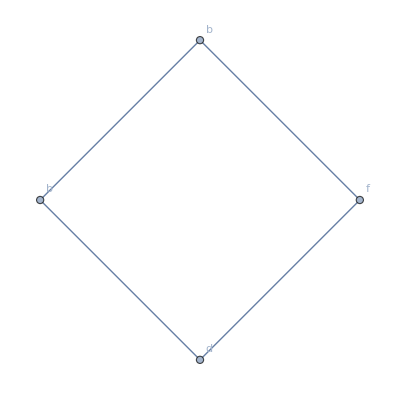
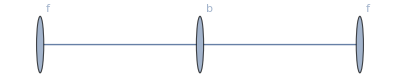
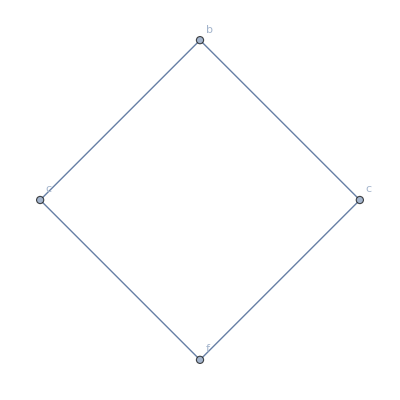
(-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-)

```mathematica
Clear[a,b,c,d,e,f]; (* These rules create a square grid. *)
Rect={
Graph[{1},{},VertexLabels->{1->a}]->Graph[{1,2,3,4},{1<->2,2<->3,3<->4,1<->4},VertexLabels->{1->b,2->d,3->c,4->d}],
Graph[{1,2},{1<->2},VertexLabels->{1->d,2->c}]->Graph[{1,2,3,4},{1<->2,2<->3,3<->4,1<->4},VertexLabels->{1->b,2->e,3->f,4->d}],
Graph[{1,2},{1<->2},VertexLabels->{1->d,2->e}]->Graph[{1,2,3,4},{1<->2,2<->3,3<->4,1<->4},VertexLabels->{1->b,2->b,3->f,4->d}],
Graph[{1,2,3},{1<->2,2<->3},VertexLabels->{1->f,2->b,3->f}]->Graph[{1,2,3,4},{1<->2,2<->3,3<->4,1<->4},VertexLabels->{1->c,2->b,3->c,4->f}],
Graph[{1,2,3},{1<->2,2<->3},VertexLabels->{1->f,2->e,3->f}]->Graph[{1,2,3,4},{1<->2,2<->3,3<->4,1<->4},VertexLabels->{1->c,2->b,3->c,4->f}]
};
Rect//MatrixForm
```

```mathematica
Rectgraph=Graph[{1},{},VertexLabels->{1->a}];
```

```mathematica
Dynamic[Rectgraph]
```

```mathematica
Do[Rectgraph=GraphGrammarSteps[Rectgraph,Rect,1],10000]
```

RandomSample::smplen: RandomSample cannot generate a sample of length 3, which is greater than the length of the sample set {1}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

MapThread::mptd: Object RandomSample[{1},3] at position {2, 2} in MapThread[Rule,{{1,2,3},RandomSample[{1},3]}] has only 0 of required 1 dimensions.

RandomSample::smplen: RandomSample cannot generate a sample of length 2, which is greater than the length of the sample set {1}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

MapThread::mptd: Object RandomSample[{1},2] at position {2, 2} in MapThread[Rule,{{1,2},RandomSample[{1},2]}] has only 0 of required 1 dimensions.

This is my second attempt at the challenge. This set of rules is supposed to create an infinitely growing grid that is a square by growing out the diagonal and then filling in. Had some issues with create squares inside and not fully filling out the square so backtracked a bit and moved on to a different strategy (the diagonal growth rule also overpowered the other rules). Also do not believe this strategy will have the correct size for amount variables and rules needed if I wanted to make a specific sized grid.

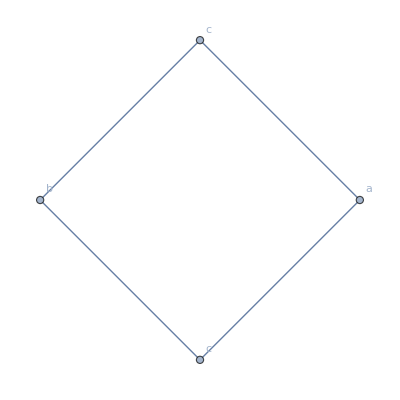
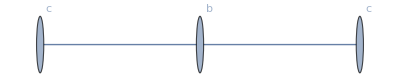
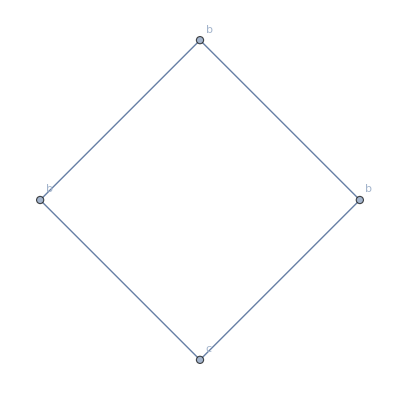
(-Graphics-→-Graphics-
-Graphics-→-Graphics-)

```mathematica
Clear[a,b,c]; (* These rules create an infinitely growing grid. *)
Diag={
Graph[{1},{},VertexLabels->{1->a}]->Graph[{1,2,3,4},{1<->2,2<->3,3<->4,1<->4},VertexLabels->{1->b,2->c,3->a,4->c}],
Graph[{1,2,3},{1<->2,2<->3},VertexLabels->{1->c,2->b,3->c}]->Graph[{1,2,3,4},{1<->2,2<->3,3<->4,1<->4},VertexLabels->{1->b,2->b,3->b,4->c}]
};
Diag//MatrixForm
```

```mathematica
Diaggraph=Graph[{1},{},VertexLabels->{1->a}];
```

```mathematica
Dynamic[Diaggraph]
```

```mathematica
Do[Diaggraph=GraphGrammarSteps[Diaggraph,Diag,1],100]
```

RandomSample::smplen: RandomSample cannot generate a sample of length 3, which is greater than the length of the sample set {1}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

MapThread::mptd: Object RandomSample[{1},3] at position {2, 2} in MapThread[Rule,{{1,2,3},RandomSample[{1},3]}] has only 0 of required 1 dimensions.

RandomSample::smplen: RandomSample cannot generate a sample of length 3, which is greater than the length of the sample set {1}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

MapThread::mptd: Object RandomSample[{1},3] at position {2, 2} in MapThread[Rule,{{1,2,3},RandomSample[{1},3]}] has only 0 of required 1 dimensions.

This is my third attempt at the challenge. This set of rules is supposed to create a single square that keeps being divided into smaller squares. This strategy seems like it will have the correct size for amount variables and rules needed to make a specific sized grid. This strategy seems to work but the random selection of vertices make it very hard to select the right things to replace for the rules with lots of vertices. Next steps would to either make a better grammar stepper or to make the rules need fewer vertices to be selected. We could then keep expanding to larger grid sizes.

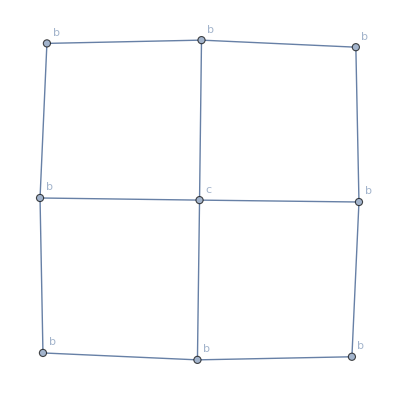
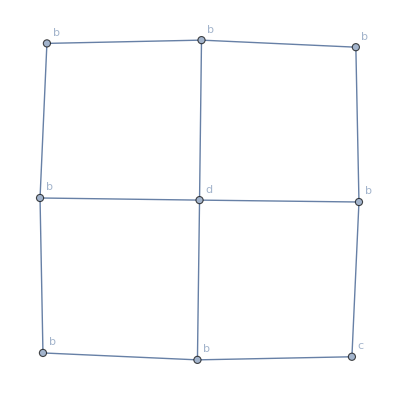
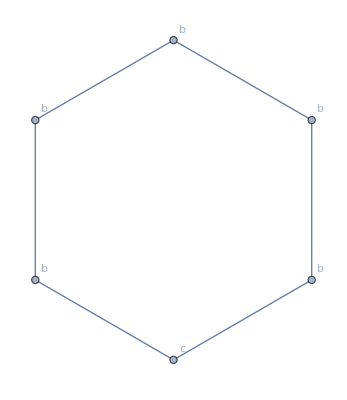
(-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-)

```mathematica
Clear[a,b,c]; (* These rules create an specific sized grid. *)
Splt={
Graph[{1},{},VertexLabels->{1->a}]->Graph[{1,2,3,4, 5, 6, 7, 8, 9},{1<->5,5<->2,5<->9,2<->6,6<->3,6<->9,3<->7,7<->4,7<->9,4<->8,8<->1,8<->9},VertexLabels->{1->b,2->b,3->b,4->b,5->b,6->b,7->b,8->b,9->c}],
Graph[{1,2,3,4},{1<->2,2<->3,3<->4,4<->1},VertexLabels->{1->b,2->b,3->b,4->c}]->Graph[{1,2,3,4, 5, 6, 7, 8, 9},{1<->5,5<->2,5<->9,2<->6,6<->3,6<->9,3<->7,7<->4,7<->9,4<->8,8<->1,8<->9},VertexLabels->{1->b,2->b,3->b,4->c,5->b,6->b,7->b,8->b,9->d}],
Graph[{1,2,3,10,4,11},{1<->2,2<->3,3<->10,10<->4,4<->11,11<->1},VertexLabels->{1->b,2->b,3->b,4->c,10->b,11->b}]->Graph[{1,2,3,4, 5, 6, 7, 8, 9},{1<->5,5<->2,5<->9,2<->6,6<->3,6<->9,3<->7,7<->4,7<->9,4<->8,8<->1,8<->9},VertexLabels->{1->b,2->b,3->b,4->c,5->b,6->b,7->b,8->b,9->d}]
};
Splt//MatrixForm
```

```mathematica
Spltgraph=Graph[{1},{},VertexLabels->{1->a}];
```

```mathematica
Dynamic[Spltgraph]
```

```mathematica
Do[Spltgraph=GraphGrammarSteps[Spltgraph,Splt,1],1000000]
```

This is my final attempt at the challenge. This set of rules is supposed to expand outwards to get the correct size for amount variables and rules needed to make a specific sized grid, and then fill in the rest of the grid after. Salvador suggested trying this idea during office hours. Didn’t spend very much time on it because wanted to work with one more model.

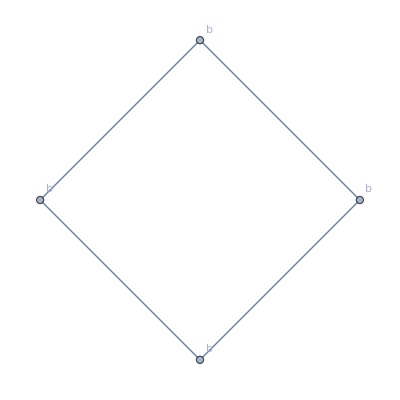
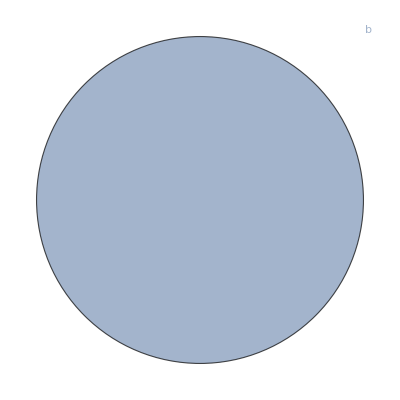
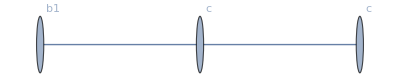
(-Graphics-→-Graphics-
-Graphics-→-Graphics-)

```mathematica
Clear[a,b,b1,c,c1,d]; (* These rules create an specific sized grid. *)
Grow={
Graph[{1},{},VertexLabels->{1->a}]->Graph[{1,2,3,4},{1<->2,2<->3,3<->4,4<->1},VertexLabels->{1->b,2->b,3->b,4->b}],
Graph[{1},{},VertexLabels->{1->b}]->Graph[{1,2,3},{1<->2,2<->3},VertexLabels->{1->b1,2->c,3->c}]
};
Grow//MatrixForm
```

```mathematica
Growgraph=Graph[{1},{},VertexLabels->{1->a}];
```

```mathematica
Dynamic[Growgraph]
```

```mathematica
Do[Growgraph=GraphGrammarSteps[Growgraph,Grow,1],100000]
```

Program 3: My third program will be creating a simple circuit binary multiplier. I enjoyed the circuits from assignment 1 so wanted to try implementing this quickly since I spend most my time on program 2.

```mathematica
CircuitWires[circuit_]:=Union[Flatten[
circuit//.{Rule[wire_,value_]:>{wire,value},(And|Or|Not|Xor|Xnor|Nand|Nor)[args___]:>{args},True|False->{}}]]
```

```mathematica
CircuitStableQ[circuit_,wirevalues_]:=AllTrue[circuit,(#[[1]]/.wirevalues)===(#[[2]]/.wirevalues)&]
```

```mathematica
CircuitStep[circuit_,wirevalues_]:=
Module[{wires=CircuitWires[circuit],state,n},
state=wires/.wirevalues; (* keep a list of wire values, as True/False in order of "wires" *)
If[!CircuitStableQ[circuit,wirevalues],
n=RandomInteger[{1,Length[state]}];(* randomly try gates until one changes *)
While[state[[n]]==(wires[[n]]/.circuit)/.wirevalues,
n=RandomInteger[{1,Length[state]}]];
state[[n]]=(wires[[n]]/.circuit)/.wirevalues
];
MapThread[Rule,{wires,state}]
]
```

```mathematica
EvaluateCircuit[circuit_,inputvalues_,outputwires_]:=
Module[{wires=CircuitWires[circuit],state,initialwirevalues,finalwirevalues},
(* initialized randomly except for the "inputs" *)
state=Map[If[BooleanQ[#],#,RandomChoice[{True,False}]]&,wires/.inputvalues];
initialwirevalues=MapThread[Rule,{wires,state}];
finalwirevalues=FixedPoint[CircuitStep[circuit,#]&,initialwirevalues];
(* format the out as rules transforming wire names to Boolean values *)
(#->(#/.finalwirevalues))&/@outputwires
]
```

Set up wires and circuit, input 1 uses a0 and a1 and input 2 uses b0 and b1, and the output goes to c0, c1, c2, c3

```mathematica
Clear[a0,a1,b0,b1,w1,w2,w3,w4,c0,c1,c2,c3];
```

```mathematica
multiplier={w1->And[a0,b1],c0->And[a0,b0],w2->And[a1,b0],w3->And[a1,b1],c1->Xor[w1,w2],w4->And[w1,w2],c2->Xor[w4,w3],c3->And[w4,w3]}
```

{w1→a0&&b1,c0→a0&&b0,w2→a1&&b0,w3→a1&&b1,c1→w1⊻w2,w4→w1&&w2,c2→w3⊻w4,c3→w4&&w3}

Test circuit on all inputs

```mathematica
{{A1,A0,B1,B0,C3,C2,C1,C0}}~Join~Flatten[Table[Boole[{a1,a0,b1,b0,c3,c2,c1,c0}]/.EvaluateCircuit[multiplier,{a1->aa1,a0->aa0,b1->bb1,b0->bb0},CircuitWires[multiplier]],
{aa1,{False,True}},{aa0,{False,True}},{bb1,{False,True}},{bb0,{False,True}}],3]//MatrixForm
```

(A1 | A0 | B1 | B0 | C3 | C2 | C1 | C0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 1)

Verify values are correct

```mathematica
(* the Hold / Release ensures that the expression is evaluated after the substitution of variable values *)
Release@Flatten[Table[Hold[FromDigits[{Boole[c3],Boole[c2],Boole[c1],Boole[c0]},2]==FromDigits[{Boole[a1],Boole[a0]},2]*FromDigits[{Boole[b1],Boole[b0]},2]]/.EvaluateCircuit[multiplier,{a1->aa1,a0->aa0,b1->bb1,b0->bb0},CircuitWires[multiplier]],
{aa1,{False,True}},{aa0,{False,True}},{bb1,{False,True}},{bb0,{False,True}}] ]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}